```mathematica
(* ::Package::*)(* ::Title::*)(*Quantum Prisoner's Dilemma:Iterative Best Response Dynamics*)(* ::Section::*)(*1. Initialization*)(*Load necessary packages and definitions.Ensure that the paths to "StrategySpaces.wl" and "QPD_dynamics.wl" are correct.*)Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\StrategySpaces.wl"];
Import["C:\\Users\\jhenry1\\Documents\\GitHub\\QM_prisoners_dilemma\\Mathematica\\QPD_dynamics.wl"];

(* ::Section::*)
(*2. Symbolic Calculation of Payoff Functions*)

(*Define the final state of the quantum game.*)
(*The `play` function likely simulates the game,taking the game's entanglement operator J and the players' strategies as input.*)
finalState=play[J[a,a,γ],su2[θ1,ϕ1,ζ1],su2[θ2,ϕ2,ζ2]]/. Conjugate->MyConj;

(*Simplify the final state expression.*)
finalState=FullSimplify[Simplify/@ComplexExpand[finalState]];

(*Symbolically compute the scores for Alice and Bob.*)
aliceSymbolicScore=(alicesScore[finalState]/. Conjugate->MyConj);
bobSymbolicScore=(bobsScore[finalState]/. Conjugate->MyConj);

(*Substitute specific game parameters.Here,we set the entanglement parameter'a' to 1 and the strategy parameter'γ' to π/4.*)
entanglementParameter=1;
strategyParameter=π/4;

aliceScoresComputed=Simplify/@ComplexExpand[aliceSymbolicScore/. {a->entanglementParameter,γ->strategyParameter}];
bobScoresComputed=Simplify/@ComplexExpand[bobSymbolicScore/. {a->entanglementParameter,γ->strategyParameter}];

(* ::Section::*)
(*3. Compiled Functions for Numerical Evaluation*)

(*Compile the symbolic score expressions for efficient numerical evaluation.*)
(*This is a key optimization for performance-critical functions like those used in NMaximize and Manipulate.*)

aliceCompiledScore=Compile[{{t1,_Real},{p1,_Real},{z1,_Real},{t2,_Real},{p2,_Real},{z2,_Real}},Evaluate[aliceScoresComputed/. {θ1->t1,ϕ1->p1,ζ1->z1,θ2->t2,ϕ2->p2,ζ2->z2}]];

bobCompiledScore=Compile[{{t1,_Real},{p1,_Real},{z1,_Real},{t2,_Real},{p2,_Real},{z2,_Real}},Evaluate[bobScoresComputed/. {θ1->t1,ϕ1->p1,ζ1->z1,θ2->t2,ϕ2->p2,ζ2->z2}]];

(*Create safe versions of the compiled functions that check for numeric inputs.*)
(*This prevents errors when symbolic values are inadvertently passed to the compiled functions.*)
safeAliceScore[t1_?NumericQ,p1_?NumericQ,z1_?NumericQ,t2_?NumericQ,p2_?NumericQ,z2_?NumericQ]:=aliceCompiledScore[t1,p1,z1,t2,p2,z2];
safeBobScore[t1_?NumericQ,p1_?NumericQ,z1_?NumericQ,t2_?NumericQ,p2_?NumericQ,z2_?NumericQ]:=bobCompiledScore[t1,p1,z1,t2,p2,z2];


(* ::Section::*)(*4. Best Response Functions (Optimized)*)Options[findAlicesBestResponse]={Method->{"RandomSearch","SearchPoints"->15},(*Faster method with fewer initial points*)PrecisionGoal->3,AccuracyGoal->3};
Options[findBobsBestResponse]={Method->{"RandomSearch","SearchPoints"->15},PrecisionGoal->3,AccuracyGoal->3};

findAlicesBestResponse[bobMove_List,opts:OptionsPattern[]]:=NMaximize[{safeAliceScore[θ1,ϕ1,ζ1,bobMove[[1]],bobMove[[2]],bobMove[[3]]],0<θ1<2 Pi,0<ϕ1<2 Pi,0<ζ1<2 Pi},{θ1,ϕ1,ζ1},Method->OptionValue[Method],PrecisionGoal->OptionValue[PrecisionGoal],AccuracyGoal->OptionValue[AccuracyGoal]];

findBobsBestResponse[aliceMove_List,opts:OptionsPattern[]]:=NMaximize[{safeBobScore[aliceMove[[1]],aliceMove[[2]],aliceMove[[3]],θ2,ϕ2,ζ2],0<θ2<2 Pi,0<ϕ2<2 Pi,0<ζ2<2 Pi},{θ2,ϕ2,ζ2},Method->OptionValue[Method],PrecisionGoal->OptionValue[PrecisionGoal],AccuracyGoal->OptionValue[AccuracyGoal]];
```

```mathematica
findBobsBestResponse[{1,2,3}]
```

OptionValue::optnf: Option name Method not found in defaults for findBobsBestResponse.

NMaximize::bdmtd: Value of option Method -> Method is not Automatic, "DifferentialEvolution", "NelderMead", "RandomSearch", or "SimulatedAnnealing".

NMaximize[{safeBobScore[1,2,3,θ2,ϕ2,ζ2],0<θ2<2 π,0<ϕ2<2 π,0<ζ2<2 π},{θ2,ϕ2,ζ2},Method→Method]

```mathematica
(* ::Section::*)(*5. Interactive Simulation (4 Iterations)*)Manipulate[Module[{initialAliceMove,initialBobMove,history,scores,bestResponseOpts},(*Faster settings for real-time slider interaction*)bestResponseOpts=ControlActive[{Method->{"RandomSearch","SearchPoints"->10},PrecisionGoal->2,AccuracyGoal->2},{Method->{"RandomSearch","SearchPoints"->25},PrecisionGoal->3,AccuracyGoal->3}];
(*Initial strategies from sliders*)initialAliceMove={th1,ph1,z1};
initialBobMove={th2,ph2,z2};
(*Generate the history of moves over 4 iterations using NestList.The state passed between iterations is {currentAliceMove,currentBobMove}.*)history=NestList[Module[{currentAlice,currentBob,nextAlice,nextBob},{currentAlice,currentBob}=#;
(*Alice calculates her best response to Bob's last move*)nextAlice=Values@Last@findAlicesBestResponse[currentBob,bestResponseOpts];
(*Bob calculates his best response to Alice's new move*)nextBob=Values@Last@findBobsBestResponse[nextAlice,bestResponseOpts];
{nextAlice,nextBob}]&,{initialAliceMove,initialBobMove},3 (*Number of iterations*)];
(*Calculate the scores at each step of the history.The resulting list of scores will be {{bob's score,alice's score},...}*)scores=Table[Module[{aliceMove,bobMove},aliceMove=history[[i,1]];
bobMove=history[[i,2]];
{safeBobScore@@Join[aliceMove,bobMove],safeAliceScore@@Join[aliceMove,bobMove]}],{i,Length[history]}];
ListPlot[scores,PlotRange->{{0,5},{0,5}},Frame->True,AspectRatio->1,PlotStyle->Arrowheads[{{0.04,0.8}}],PlotMarkers->{Graphics[Disk[]],.03},FrameLabel->{"Bob's Score","Alice's Score"},PlotLabel->"Iterative Score Dynamics (4 Iterations)",Joined->True]],(*Sliders for initial strategy parameters*){{th1,Pi/2,"Alice θ1"},0,2 Pi},{{ph1,Pi/2,"Alice ϕ1"},0,2 Pi},{{z1,Pi/2,"Alice ζ1"},0,2 Pi},Pane["",ImageSize->{280,2},BaseStyle->"Gray"],{{th2,Pi/2,"Bob θ2"},0,2 Pi},{{ph2,Pi/2,"Bob ϕ2"},0,2 Pi},{{z2,Pi/2,"Bob ζ2"},0,2 Pi},TrackedSymbols:>{th1,ph1,z1,th2,ph2,z2}]
```

```mathematica
(* ::Section::*)(*6. Symmetric Strategy Score Explorer (Plotted vs.Zeta)*)Manipulate[Plot[(*Evaluate the scores as a function of z inside the Plot*){safeAliceScore[th,ph,z,th,ph,z],safeBobScore[th,ph,z,th,ph,z]},{z,0,2 Pi},(*Plot over the full range of z*)(*Plotting Options*)Frame->True,PlotRange->{{0,2 Pi},{0,5}},PlotLegends->{"Alice's Score","Bob's Score"},FrameLabel->{"ζ (Zeta)","Score"}],(*Sliders for the shared strategy parameters that are NOT being plotted*){{th,Pi/2,"θ (Theta)"},0,2 Pi},{{ph,Pi/2,"φ (Phi)"},0,2 Pi},TrackedSymbols:>{th,ph}]
```

```mathematica
(* ::Section::*)(*7. 3D Score Explorer (Phi vs.Zeta)*)Manipulate[Plot3D[(*The score function to plot.Alice's and Bob's are identical here.*)safeAliceScore[th,ph,z,th,ph,z],(*Define the two variables for the plot axes*){ph,0,2 Pi},{z,0,2 Pi},(*Plotting Options*)PlotRange->{0,5},AxesLabel->{"φ (Phi)","ζ (Zeta)","Score"},ImageSize->Large,ColorFunction->"SolarColors"],(*Slider to control the remaining theta parameter*){{th,Pi/2,"θ (Theta)"},0,2 Pi},TrackedSymbols:>{th}]
```

```mathematica
(* ::Section::*)(*8. 3D Density Plot of Alice's Score vs.Her Strategy Space*)Manipulate[DensityPlot3D[(*Alice's score as a function of her own strategy variables*)safeAliceScore[th1,ph1,z1,th2,ph2,z2],(*Define the 3D space of Alice's variables to plot over*){th1,0,2 Pi},{ph1,0,2 Pi},{z1,0,2 Pi},(*Plotting Options*)PlotLegends->Automatic,(*Adds the color bar legend*)(*OpacityFunction->0.1,*)(*Makes the lower-score regions more transparent*)AxesLabel->{"Alice θ1","Alice φ1","Alice ζ1"},ImageSize->Large,ColorFunction->"Rainbow"],(*Sliders to control Bob's fixed strategy*){{th2,Pi/2,"Bob θ2"},0,2 Pi},{{ph2,Pi/2,"Bob φ2"},0,2 Pi},{{z2,Pi/2,"Bob ζ2"},0,2 Pi},TrackedSymbols:>{th2,ph2,z2}]
```

```mathematica
(* ::Section::*)(*9. Isosurface Plot of Alice's Score at 3*)Manipulate[ContourPlot3D[(*Set the function equal to the desired contour value*)safeAliceScore[th1,ph1,z1,th2,ph2,z2],(*Define the 3D space of Alice's variables*){th1,0,2 Pi},{ph1,0,Pi},{z1,0, Pi},(*Plotting Options*)AxesLabel->{"Alice θ1","Alice φ1","Alice ζ1"},ImageSize->Large,ContourStyle->Directive[Opacity[0.6],Specularity[White,30]],Mesh->None (*Typically looks cleaner for a single surface*)],(*Sliders to control Bob's fixed strategy*){{th2,Pi/2,"Bob θ2"},0,2 Pi},{{ph2,Pi/2,"Bob φ2"},0,2 Pi},{{z2,Pi/2,"Bob ζ2"},0,2 Pi},TrackedSymbols:>{th2,ph2,z2}]
```

```mathematica
(* ::Section::*)(*10. Side-by-Side Density Plots of Player Scores*)Manipulate[Row[{(*Plot for Alice's Score*)DensityPlot3D[safeAliceScore[th1,ph1,z1,th2,ph2,z2],{th1,0,2 Pi},{ph1,0,2 Pi},{z1,0,2 Pi},PlotLabel->"Alice's Score",PlotLegends->Automatic,AxesLabel->{"Alice θ1","Alice φ1","Alice ζ1"},ImageSize->Medium,ColorFunction->"Rainbow"],(*Plot for Bob's Score*)DensityPlot3D[safeBobScore[th1,ph1,z1,th2,ph2,z2],{th1,0,2 Pi},{ph1,0,2 Pi},{z1,0,2 Pi},PlotLabel->"Bob's Score",PlotLegends->Automatic,AxesLabel->{"Alice θ1","Alice φ1","Alice ζ1"},ImageSize->Medium,ColorFunction->"Rainbow"]}],(*Sliders to control Bob's fixed strategy*){{th2,Pi/2,"Bob θ2"},0,2 Pi},{{ph2,Pi/2,"Bob φ2"},0,2 Pi},{{z2,Pi/2,"Bob ζ2"},0,2 Pi},TrackedSymbols:>{th2,ph2,z2}]
```

```mathematica
findNashEquilibrium::usage="findNashEquilibrium[aliceScore, bobScore, opts] finds a validated local Nash Equilibrium.
  It checks the equilibrium condition numerically using FindMaximum.";
(*The local solver from our last conversation.It checks a single start point.*)findNashEquilibrium[aliceScore_Function,bobScore_Function,opts___?OptionQ]:=Module[{p1vars,p2vars,allvars,gradA,gradB,focs,startPoint,criticalPoint,aliceVarsAtCrit,bobVarsAtCrit,aliceCheck,bobCheck,isNash},p1vars={th1,ph1,z1};p2vars={th2,ph2,z2};allvars=Join[p1vars,p2vars];
startPoint="StartPoint"/. {opts}/. {"StartPoint"->RandomReal[{0,2 Pi},6]};
gradA=Grad[aliceScore[th1,ph1,z1,th2,ph2,z2],p1vars];
gradB=Grad[bobScore[th1,ph1,z1,th2,ph2,z2],p2vars];
focs=Join[Thread[gradA==0],Thread[gradB==0]];
criticalPoint=Quiet@Check[FindRoot[focs,Transpose[{allvars,startPoint}]],$Failed];
If[criticalPoint===$Failed||Not[And@@Thread[0<=allvars<=2 Pi]/. criticalPoint],Return[$Failed]];
aliceVarsAtCrit=p1vars/. criticalPoint;
bobVarsAtCrit=p2vars/. criticalPoint;
aliceCheck=FindMaximum[{aliceScore[th1,ph1,z1,Sequence@@bobVarsAtCrit],And@@Thread[0<=p1vars<=2 Pi]},Evaluate[Sequence@@Transpose[{p1vars,aliceVarsAtCrit}]]];
bobCheck=FindMaximum[{bobScore[Sequence@@aliceVarsAtCrit,th2,ph2,z2],And@@Thread[0<=p2vars<=2 Pi]},Evaluate[Sequence@@Transpose[{p2vars,bobVarsAtCrit}]]];
isNash=(Abs[First[aliceCheck]-(aliceScore[##]&@@Join[aliceVarsAtCrit,bobVarsAtCrit])]<1*^-6)&&(Abs[First[bobCheck]-(bobScore[##]&@@Join[aliceVarsAtCrit,bobVarsAtCrit])]<1*^-6);
If[isNash,Return[criticalPoint],Return[$Failed]]];

(*The grid search wrapper function*)
gridSearchNash::usage="gridSearchNash[aliceScore, bobScore, n] performs a grid search for Nash Equilibria.
  - n: The number of grid points for each of the 6 dimensions. Total checks = n^6.";

gridSearchNash[aliceScore_Function,bobScore_Function,n_Integer?Positive]:=Module[{gridPoints,results,uniqueSolutions},(*1. Generate the grid of starting points*)If[n==1,gridPoints={Table[Pi,{6}]},(*Special case for a single central point*)gridPoints=Tuples[Subdivide[0,2 Pi,n-1],6]];
Print["Generated ",Length[gridPoints]," starting points for the grid search."];
(*2. Run the local solver from each point in parallel*)results=ParallelMap[findNashEquilibrium[aliceScore,bobScore,StartPoint->#]&,gridPoints];
(*3. Filter out failures and remove duplicate solutions*)uniqueSolutions=DeleteDuplicates[Select[results,#=!=$Failed&],(*Two solutions are considered duplicates if their points are very close*)(Norm[(Values[#1]-Values[#2])]<1*^-4)&];
Print["Found ",Length[uniqueSolutions]," unique Nash Equilibria."];
Return[uniqueSolutions];]
```

```mathematica
(*This will take some time to run*)foundEquilibria=gridSearchNash[safeAliceScore[##]&,safeBobScore[##]&,3]
```

Generated 729 starting points for the grid search.

Found 3 unique Nash Equilibria.

{{th1→4.70836,ph1→3.14163,z1→4.71243,th2→3.14163,ph2→4.71115,z2→3.14163},{th1→2.92022×10^-7,ph1→1.56841,z1→2.80688×10^-7,th2→3.14159,ph2→1.56425,z2→3.14159},{th1→3.14159,ph1→1.56504,z1→3.14159,th2→3.14159,ph2→4.70496,z2→3.14159}}

```mathematica
safeAliceScore@@foundEquilibria[[2]]/.(_->var_)->var
safeBobScore@@foundEquilibria[[2]]/.(_->var_)->var
```

3.

3.

```mathematica
safeAliceScore@@foundEquilibria[[3]]/.(_->var_)->var
safeBobScore@@foundEquilibria[[3]]/.(_->var_)->var
```

3.

3.

```mathematica
foundEquilibria[[3]]/.(_->var_)->var
```

{3.14159,1.56504,3.14159,3.14159,4.70496,3.14159}

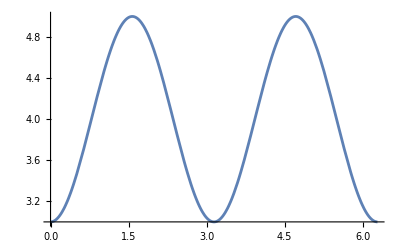

```mathematica
Plot[safeBobScore[3.1415915819350206,1.5650360608222216,3.141593679047994,0,0,z],{z,0,2Pi}]
```